Edit the Circle’s radius in the generalized function

```mathematica
Animate[
Graphics[
{
Line[{{0,0},{5*Cos[time],5*Sin[time]}}],
Circle[{0,0},5],

Circle[{5*Cos[time],5*Sin[time]},3],
Line[{{5*Cos[time],5*Sin[time]},{3*Cos[2time]+5*Cos[time],3*Sin[2time]+5*Sin[time]}}],

Circle[{3*Cos[2time]+5*Cos[time],3*Sin[2time]+5*Sin[time]},2],
Line[{{3*Cos[2time]+5*Cos[time],3*Sin[2time]+5*Sin[time]},{5*Cos[time]+3*Cos[2time]+2Cos[3time],5*Sin[time]+3*Sin[2time]+2Sin[3time]}}],

Circle[{5*Cos[time]+3*Cos[2time]+2Cos[3time],5*Sin[time]+3*Sin[2time]+2Sin[3time]},1],
Line[{{5*Cos[time]+3*Cos[2time]+2Cos[3time],5*Sin[time]+3*Sin[2time]+2Sin[3time]},{5*Cos[time]+3*Cos[2time]+2Cos[3time]+Cos[4time],5*Sin[time]+3*Sin[2time]+2Sin[3time]+Sin[4time]}}],

Circle[{5*Cos[time]+3*Cos[2time]+2Cos[3time]+Cos[4time],5*Sin[time]+3*Sin[2time]+2Sin[3time]+Sin[4time]},0.5],
Line[{{5*Cos[time]+3*Cos[2time]+2Cos[3time]+Cos[4time],5*Sin[time]+3*Sin[2time]+2Sin[3time]+Sin[4time]},{5*Cos[time]+3*Cos[2time]+2Cos[3time]+Cos[4time]+0.5Cos[5time],5*Sin[time]+3*Sin[2time]+2Sin[3time]+Sin[4time]+0.5Sin[5time]}}]
}
],
{time,0,2*Pi},AnimationRunning->False]
```

```mathematica
fourierSeries[numberCircles_,radiusList_List,frequencyList_List]:=
MapThread[#1*Cos[#2*time]&,{radiusList,frequencyList}]
Animate[
Graphics[
{
Line[{{0,0},{5*Cos[time],5*Sin[time]}}],
Circle[{0,0},5],

Circle[{5*Cos[time],5*Sin[time]},3],
Line[{{5*Cos[time],5*Sin[time]},{3*Cos[2time]+5*Cos[time],3*Sin[2time]+5*Sin[time]}}],

Circle[{3*Cos[2time]+5*Cos[time],3*Sin[2time]+5*Sin[time]},2],
Line[{{3*Cos[2time]+5*Cos[time],3*Sin[2time]+5*Sin[time]},{5*Cos[time]+3*Cos[2time]+2Cos[3time],5*Sin[time]+3*Sin[2time]+2Sin[3time]}}],

Circle[{5*Cos[time]+3*Cos[2time]+2Cos[3time],5*Sin[time]+3*Sin[2time]+2Sin[3time]},1],
Line[{{5*Cos[time]+3*Cos[2time]+2Cos[3time],5*Sin[time]+3*Sin[2time]+2Sin[3time]},{5*Cos[time]+3*Cos[2time]+2Cos[3time]+Cos[4time],5*Sin[time]+3*Sin[2time]+2Sin[3time]+Sin[4time]}}],

Circle[{5*Cos[time]+3*Cos[2time]+2Cos[3time]+Cos[4time],5*Sin[time]+3*Sin[2time]+2Sin[3time]+Sin[4time]},0.5],
Line[{{5*Cos[time]+3*Cos[2time]+2Cos[3time]+Cos[4time],5*Sin[time]+3*Sin[2time]+2Sin[3time]+Sin[4time]},{5*Cos[time]+3*Cos[2time]+2Cos[3time]+Cos[4time]+0.5Cos[5time],5*Sin[time]+3*Sin[2time]+2Sin[3time]+Sin[4time]+0.5Sin[5time]}}]
}
],
{time,0,2*Pi},AnimationRunning->False]
```

```mathematica
?Part
```

```mathematica
fourierSeries[numberCircles_,radiusList_List,frequencyList_List]:=
MapThread[{#1*Cos[#2*time],#1*Sin[#2*time]}&,{radiusList,frequencyList}]
```

```mathematica
testCircleList=fourierSeries[5,{5,4,3,2,1},{1,2,3,4,5}]
```

{{5 Cos[time],5 Sin[time]},{4 Cos[2 time],4 Sin[2 time]},{3 Cos[3 time],3 Sin[3 time]},{2 Cos[4 time],2 Sin[4 time]},{Cos[5 time],Sin[5 time]}}

```mathematica
Table[{{5 Cos[time],5 Sin[time]},{4 Cos[2 time],4 Sin[2 time]},{3 Cos[3 time],3 Sin[3 time]},{2 Cos[4 time],2 Sin[4 time]},{Cos[5 time],Sin[5 time]}}[[;;n]],{n,1,Length[testCircleList]}]
```

{{{5 Cos[time],5 Sin[time]}},{{5 Cos[time],5 Sin[time]},{4 Cos[2 time],4 Sin[2 time]}},{{5 Cos[time],5 Sin[time]},{4 Cos[2 time],4 Sin[2 time]},{3 Cos[3 time],3 Sin[3 time]}},{{5 Cos[time],5 Sin[time]},{4 Cos[2 time],4 Sin[2 time]},{3 Cos[3 time],3 Sin[3 time]},{2 Cos[4 time],2 Sin[4 time]}},{{5 Cos[time],5 Sin[time]},{4 Cos[2 time],4 Sin[2 time]},{3 Cos[3 time],3 Sin[3 time]},{2 Cos[4 time],2 Sin[4 time]},{Cos[5 time],Sin[5 time]}}}

```mathematica
Plus@@@
{
{
{5 Cos[time],5 Sin[time]}
},
{
{5 Cos[time],5 Sin[time]},{4 Cos[2 time],4 Sin[2 time]}
},
{
{5 Cos[time],5 Sin[time]},{4 Cos[2 time],4 Sin[2 time]},{3 Cos[3 time],3 Sin[3 time]}
},
{
{5 Cos[time],5 Sin[time]},{4 Cos[2 time],4 Sin[2 time]},{3 Cos[3 time],3 Sin[3 time]},{2 Cos[4 time],2 Sin[4 time]}
},
{
{5 Cos[time],5 Sin[time]},{4 Cos[2 time],4 Sin[2 time]},{3 Cos[3 time],3 Sin[3 time]},{2 Cos[4 time],2 Sin[4 time]},{Cos[5 time],Sin[5 time]}
}
}
```

{{5 Cos[time],5 Sin[time]},{5 Cos[time]+4 Cos[2 time],5 Sin[time]+4 Sin[2 time]},{5 Cos[time]+4 Cos[2 time]+3 Cos[3 time],5 Sin[time]+4 Sin[2 time]+3 Sin[3 time]},{5 Cos[time]+4 Cos[2 time]+3 Cos[3 time]+2 Cos[4 time],5 Sin[time]+4 Sin[2 time]+3 Sin[3 time]+2 Sin[4 time]},{5 Cos[time]+4 Cos[2 time]+3 Cos[3 time]+2 Cos[4 time]+Cos[5 time],5 Sin[time]+4 Sin[2 time]+3 Sin[3 time]+2 Sin[4 time]+Sin[5 time]}}

```mathematica
fourierSeries[numberCircles_,radiusList_List,frequencyList_List]:=
MapThread[{#1*Cos[#2*time],#1*Sin[#2*time]}&,{radiusList,frequencyList}]
```

```mathematica
fourierSeriesCoordinates[numberCircles_,radiusList_List,frequencyList_List]:=
Plus@@@Table[MapThread[{#1*Cos[#2*time],#1*Sin[#2*time]}&,{radiusList,frequencyList}]
[[;;n]],{n,1,Length[MapThread[{#1*Cos[#2*time],#1*Sin[#2*time]}&,{radiusList,frequencyList}]]}]//Prepend[{0,0}]
```

```mathematica
fourierSeriesGraphics//Clear
```

```mathematica
Partition[fourierSeriesCoordinates[5,{5,4,3,2,1},{1,2,3,4,5}],2,1]
```

{{{0,0},{5 Cos[time],5 Sin[time]}},{{5 Cos[time],5 Sin[time]},{5 Cos[time]+4 Cos[2 time],5 Sin[time]+4 Sin[2 time]}},{{5 Cos[time]+4 Cos[2 time],5 Sin[time]+4 Sin[2 time]},{5 Cos[time]+4 Cos[2 time]+3 Cos[3 time],5 Sin[time]+4 Sin[2 time]+3 Sin[3 time]}},{{5 Cos[time]+4 Cos[2 time]+3 Cos[3 time],5 Sin[time]+4 Sin[2 time]+3 Sin[3 time]},{5 Cos[time]+4 Cos[2 time]+3 Cos[3 time]+2 Cos[4 time],5 Sin[time]+4 Sin[2 time]+3 Sin[3 time]+2 Sin[4 time]}},{{5 Cos[time]+4 Cos[2 time]+3 Cos[3 time]+2 Cos[4 time],5 Sin[time]+4 Sin[2 time]+3 Sin[3 time]+2 Sin[4 time]},{5 Cos[time]+4 Cos[2 time]+3 Cos[3 time]+2 Cos[4 time]+Cos[5 time],5 Sin[time]+4 Sin[2 time]+3 Sin[3 time]+2 Sin[4 time]+Sin[5 time]}}}

```mathematica
ClearAll[fourierSeriesGraphics]
fourierSeriesCoordinates[numberCircles_,radiusList_List,frequencyList_List]:=
With[{protoList=MapThread[{#1*Cos[#2*time],#1*Sin[#2*time]}&,{radiusList,frequencyList}]},
Plus@@@Table[protoList[[;;n]],
{n,1,Length[protoList]}]//Prepend[{0,0}]]

fourierSeriesGraphics[numberCircles_,radiusList_List,frequencyList_List]:=With[{coordinateList=Partition[fourierSeriesCoordinates[numberCircles,radiusList,frequencyList],2,1],protoList=fourierSeriesCoordinates[numberCircles,radiusList,frequencyList],circleList=Apply[,]},
Print[coordinateList];

Animate[
Graphics[
{#1,#2}],{time,0,2*Pi},AnimationRunning->False]&@Evaluate[(Line[#1]&/@coordinateList),(Circle[#1]&/@protoList)]
]
```

```mathematica
fourierSeriesGraphics[5,{5,4,3,2,1},{1,2,3,4,5}]
```

{{{0,0},{5 Cos[time],5 Sin[time]}},{{5 Cos[time],5 Sin[time]},{5 Cos[time]+4 Cos[2 time],5 Sin[time]+4 Sin[2 time]}},{{5 Cos[time]+4 Cos[2 time],5 Sin[time]+4 Sin[2 time]},{5 Cos[time]+4 Cos[2 time]+3 Cos[3 time],5 Sin[time]+4 Sin[2 time]+3 Sin[3 time]}},{{5 Cos[time]+4 Cos[2 time]+3 Cos[3 time],5 Sin[time]+4 Sin[2 time]+3 Sin[3 time]},{5 Cos[time]+4 Cos[2 time]+3 Cos[3 time]+2 Cos[4 time],5 Sin[time]+4 Sin[2 time]+3 Sin[3 time]+2 Sin[4 time]}},{{5 Cos[time]+4 Cos[2 time]+3 Cos[3 time]+2 Cos[4 time],5 Sin[time]+4 Sin[2 time]+3 Sin[3 time]+2 Sin[4 time]},{5 Cos[time]+4 Cos[2 time]+3 Cos[3 time]+2 Cos[4 time]+Cos[5 time],5 Sin[time]+4 Sin[2 time]+3 Sin[3 time]+2 Sin[4 time]+Sin[5 time]}}}

```mathematica
?Circle
```

```mathematica
list={1,2,3,4,5}
list[[#1]]&/@Length[list]
```

{1,2,3,4,5}

5

```mathematica
testList=Partition[fourierSeriesCoordinates[5,{5,4,3,2,1},{1,2,3,4,5}],2,1]
```

{{{0,0},{5 Cos[time],5 Sin[time]}},{{5 Cos[time],5 Sin[time]},{5 Cos[time]+4 Cos[2 time],5 Sin[time]+4 Sin[2 time]}},{{5 Cos[time]+4 Cos[2 time],5 Sin[time]+4 Sin[2 time]},{5 Cos[time]+4 Cos[2 time]+3 Cos[3 time],5 Sin[time]+4 Sin[2 time]+3 Sin[3 time]}},{{5 Cos[time]+4 Cos[2 time]+3 Cos[3 time],5 Sin[time]+4 Sin[2 time]+3 Sin[3 time]},{5 Cos[time]+4 Cos[2 time]+3 Cos[3 time]+2 Cos[4 time],5 Sin[time]+4 Sin[2 time]+3 Sin[3 time]+2 Sin[4 time]}},{{5 Cos[time]+4 Cos[2 time]+3 Cos[3 time]+2 Cos[4 time],5 Sin[time]+4 Sin[2 time]+3 Sin[3 time]+2 Sin[4 time]},{5 Cos[time]+4 Cos[2 time]+3 Cos[3 time]+2 Cos[4 time]+Cos[5 time],5 Sin[time]+4 Sin[2 time]+3 Sin[3 time]+2 Sin[4 time]+Sin[5 time]}}}

```mathematica
Animate[
Graphics[
#1],{time,0,2*Pi},AnimationRunning->False]&@Evaluate@(Line[#1]&/@testList)
```

```mathematica
?Apply
```

```mathematica
Animate[
Graphics[
{
Line[{{0,0},{5*Cos[time],5*Sin[time]},{3*Cos[2time]+5*Cos[time],3*Sin[2time]+5*Sin[time]},{5*Cos[time]+3*Cos[2time]+2Cos[3time],5*Sin[time]+3*Sin[2time]+2Sin[3time]},{5*Cos[time]+3*Cos[2time]+2Cos[3time]+Cos[4time],5*Sin[time]+3*Sin[2time]+2Sin[3time]+Sin[4time]},{5*Cos[time]+3*Cos[2time]+2Cos[3time]+Cos[4time]+0.5Cos[5time],5*Sin[time]+3*Sin[2time]+2Sin[3time]+Sin[4time]+0.5Sin[5time]}
}],
Circle[{0,0},5],

Circle[{5*Cos[time],5*Sin[time]},3],

Circle[{3*Cos[2time]+5*Cos[time],3*Sin[2time]+5*Sin[time]},2],

Circle[{5*Cos[time]+3*Cos[2time]+2Cos[3time],5*Sin[time]+3*Sin[2time]+2Sin[3time]},1],


Circle[{5*Cos[time]+3*Cos[2time]+2Cos[3time]+Cos[4time],5*Sin[time]+3*Sin[2time]+2Sin[3time]+Sin[4time]},0.5],
}
],
{time,0,2*Pi},AnimationRunning->False]
```

```mathematica
ClearAll[fourierSeriesGraphicsV2]
fourierSeriesCoordinates[numberCircles_,radiusList_List,frequencyList_List]:=
	With[
		{protoList=MapThread[
						{#1*Cos[#2*time],#1*Sin[#2*time]}&,{radiusList,frequencyList}
					]
				},
		Plus@@@Table[protoList[[;;n]],
		{n,1,Length[protoList]}]//Prepend[{0,0}]
]

fourierSeriesGraphicsV2[numberCircles_,radiusList_List,frequencyList_List]:=
	With[
		{
			coordinateList=fourierSeriesCoordinates[numberCircles,radiusList,frequencyList],
			protoList=fourierSeriesCoordinates[numberCircles,radiusList,frequencyList],
			circleList=Evaluate[
					MapThread[
						Circle,{
							Drop[fourierSeriesCoordinates[numberCircles,radiusList,frequencyList],-1],
							radiusList}
						]
					]
		},
	Print[coordinateList];

	Animate[
		Graphics[{#1,#2}],
	{time,0,2*Pi},
	AnimationRunning->False]&@Evaluate[
		(Line[coordinateList]),(circleList)
	]
]
```

```mathematica
Evaluate[
					MapThread[
						Circle,{
							fourierSeriesCoordinates[numberCircles,radiusList,frequencyList],
							radiusList}
						]
					]
```

MapThread::mptd: Object fourierSeriesCoordinates[numberCircles,radiusList,frequencyList] at position {2, 1} in MapThread[Circle,{fourierSeriesCoordinates[numberCircles,radiusList,frequencyList],radiusList}] has only 0 of required 1 dimensions.

MapThread[Circle,{fourierSeriesCoordinates[numberCircles,radiusList,frequencyList],radiusList}]

```mathematica
MapThread[Circle,{coordinateList,radiusList}]
```

```mathematica
fourierSeriesGraphicsV2[5,{5,4,3,2,1},{1,2,3,4,5}]
```

{{0,0},{5 Cos[time],5 Sin[time]},{5 Cos[time]+4 Cos[2 time],5 Sin[time]+4 Sin[2 time]},{5 Cos[time]+4 Cos[2 time]+3 Cos[3 time],5 Sin[time]+4 Sin[2 time]+3 Sin[3 time]},{5 Cos[time]+4 Cos[2 time]+3 Cos[3 time]+2 Cos[4 time],5 Sin[time]+4 Sin[2 time]+3 Sin[3 time]+2 Sin[4 time]},{5 Cos[time]+4 Cos[2 time]+3 Cos[3 time]+2 Cos[4 time]+Cos[5 time],5 Sin[time]+4 Sin[2 time]+3 Sin[3 time]+2 Sin[4 time]+Sin[5 time]}}

```mathematica
Animate[
Graphics[
#1],{time,0,2*Pi},AnimationRunning->False]&@Evaluate[Line[fourierSeriesCoordinates[5,{5,4,3,2,1},{1,2,3,4,5}]]]
```

```mathematica
?MapThread
```

```mathematica
Evaluate[
		(Line[coordinateList]),
		(MapThread[Circle,{coordinateList,radiusList}])
	]
```

MapThread::mptd: Object coordinateList at position {2, 1} in MapThread[Circle,{coordinateList,radiusList}] has only 0 of required 1 dimensions.

Sequence[Line[coordinateList],MapThread[Circle,{coordinateList,radiusList}]]


{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Graphics[#1]&/@MapThread[Circle,{{{0,0},{1,1}{2,2},{3,3},{4,4},{5,5}},{1,2,3,4,5}}]
```

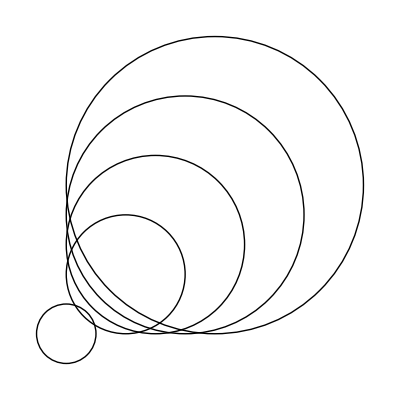

```mathematica
Graphics[MapThread[Circle,{coordinateList,radiusList}]]
```

```mathematica
?FourierTransform
```